# MATH7501 Practical 9 (Week 10), Semester 1-2021

## Topic: Sequences & Series, Limits and Derivatives

Author:  Aminath Shausan
Date: 7-05-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with units 5 to 8 contents  of the reading materials for MATH7501

# Resources

Chapters 5 to 8 of course reader

# Q1 Limit

Calculate limit_(x → Infinity) sin(e^-x) and explain why this is true

lim_(x→∞) e^-x =0. As  sin(0) is continuous,  lim_(x→∞) sin(e^-x) =0 (see page 105 of course reader for the concept of limit of composite functions).

An illustration of this limit is given below.

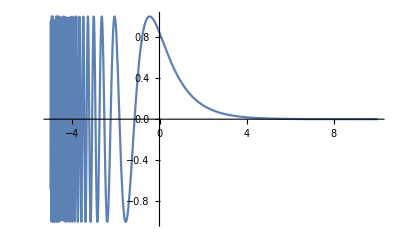

```mathematica
Plot[Sin[Exp[-x]], {x, -5, 10}]
```

# Q2 Limit

Calculate limit_(x → Infinity) 1/(cos(x) +x)

Note that -1≤ cos(x)≤ 1. So adding x to each term of the inequality  gives -1 +x≤ cos(x)+x ≤ 1+x.
For x> 1 ,  1/(1 +x)≤ 1/(cos(x)+x)≤ 1/(x-1)
As limit_(x→ ∞) 1/(-1 +x) =0   and limit_(x→ ∞) 1/(1 +x) =0  , by the sqeez theorem,   limit_(x → Infinity) 1/(cos(x) +x) =0. 

An illustration of this concept is given below.

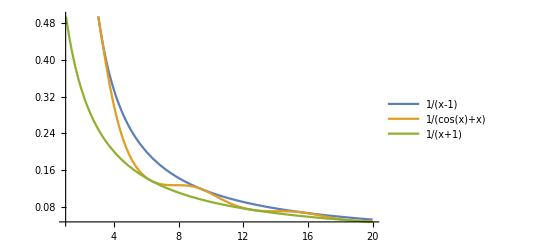

```mathematica
Plot[{1/(x-1),1/(Cos[x]+x),1/(x+1)},{x,1,20}, PlotLegends->"Expressions"]
```

# Q3 Continuous function

Consider the function 
f(x) = {(sin(x))/x          , x>0
1       ,x≤0          
 Show that this function is continuous for all x.

Hint: Continuous at a point (see Section 6.4, Definition 12)
              Continuous on interval (see pg 104)
f(x) is continuous everywhere except, possibly, at x=0. So check continuity at x=0, using Definition 12.
Check: (1) Is f(0) defined?
 This condition is satisfied  since f(0) =1.
                (2) Does limit_(x→ 0)f(0) exist? 
limit_(x→ 0^-)f(x) = f(0) =1 and limit_(x→ 0^+)f(x) = sin(x)/x =1 . So limit_(x→ 0)f(x) =1
        (3) Is limit_(x→ 0)f(x) = f(0)?
limit_(x→ 0)f(x) = 1  = f(0), so this condition is satisfied.
Thus f(x) is continuous at x=0, and hence is continuous at all x. 

The plot below shows graph of f(x) for x between -3 and 10, for illustration. It is clear from the graph that f(x) is continuous within the chosen interval

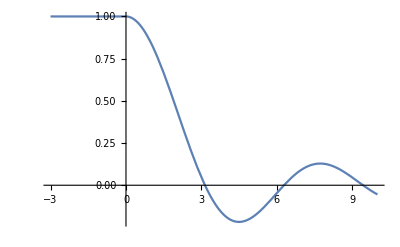

```mathematica
Plot[Piecewise[{{1,x≤0},{Sin[x]/x,x>0}}],{x,-3,10}]
```

# Q4 IVT and MVT

a) Consider the function f(x)=x^4+x+1. Show that this function does not cross the x-axis.

Step 1: Show that there is only one critical point by solving  f'(x) =0 for x
        4 x^3+1 =0 gives x=  (-1/4)^(1/3) as the only critical point.

Step 2:find f''(x) and show that  the critical point is global minimum 
         f''(x) = 12 x^2>0 for  x =  (-1/4)^(1/3). Thus the critical point is a global minimum. 
step 3: find f(x) at x=  (-1/4)^(1/3).
f( (-1/4)^(1/3)) = ((-1/4)^(1/3))^4 +(-1/4)^(1/3)+1 >0 
Therefore, f(x) does not cross the x-axis.

b)Consider the new function f(x)=x^4+x-1. Show that there are exactly two solutions to f(x)=0,using Intermediate Value Theorem (IVT)and Mean Value Theorem (MVT).

```mathematica
IVT (look at pg 105)
MVT (look at pg 115)
```

Step 1: Use IVT to get an idea of how many roots 
f(0) = -1, f(1) = 1, f(-2)=13. 
So by IVT there exists at least one root in the interval (-2, 0)and at least one root in the interal (0, 1).This means there exists at least two roots of f(x).

Step 2: Use the MVT to show that there are exactly 2 roots
Suppose there are at least three distinct roots (say x1< x2<x3). Then by the MVT,
there exists a number c in (x1, x2) such that f'(c) =0 and 
there exists a number d in (x2, x3) such that f'(d) =0
But f'(x) =4 x^3 +1 and f'(x) =0 gives 4 x^3 +1=0, x = (-1/4)^(1/3) (only one root). 
This contradicts to the assumption of having at last 3 roots. Thus there must be only 2 roots.

# Q5 Series

Determine if the following sums converge or not. If they do,work out their limit
a) ∑_(n=1)^∞ n^(2/e)

∑_(n=1)^∞ n^(2/e) =∑_(n=1)^∞ 1/n^(-2/e) diverges by the p-series test with p = -2/e

(b)∑_(n=0)^∞ (π -e)^n

∑_(n=0)^∞ (π -e)^n  converges to 1/(1+e-π) by the Geometric series test with a =1 and r = π -e